```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/gabrielefranciolini/Library/CloudStorage/GoogleDrive-gabriele.franciolini@uniroma1.it/My Drive/Past_Projects/2022/PBH_AsteroidMass_mergers/Plot_results

```mathematica
lp=100;
rp=20;
```

### Preliminary commands

```mathematica
SetOptions[EvaluationNotebook[],"ShowGroupOpener"->True];
```

```mathematica
logsample[a_,b_,n_]:=Exp[Range[Log[a//N],Log[b],Log[b/a]/n]]
```

```mathematica
fontLaTeXstyle={"CMU Serif","Latin Modern Roman"}[[1]];
(*CubaDirectory="/Users/gabrielefranciolini/Dropbox/Macbook/Mathematica/Packages/";*)
(*Install[ToString[CubaDirectory<>"Cuba-4.2/Divonne"]];
Install[ToString[CubaDirectory<>"Cuba-4.2/Suave"]];
Install[ToString[CubaDirectory<>"Cuba-4.2/Vegas"]];*)
```

#### Automatic save of the notebook

```mathematica
(*memory:=Print["Memory in use: ",MemoryInUse[]/1024.^2," Mb"]*)
```

This command saves automatically the notebook every 3 minutes, since I got sick of losing my modifications because Mathematica crashed and I haven’t saved in a while:

```mathematica
(*startsaveTask:=Block[{saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],3*60]},StartScheduledTask[saveTask]]*)
```

```mathematica
(*startsaveTask*)
```

To block this automatic saving task:

```mathematica
(*stopsaveTask:=RemoveScheduledTask[CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],3*60]]*)
```

#### MaTeX

To install MaTeX, a cool add-on to have LATEX labels, run this command after having downloaded the package from here:
https://github.com/szhorvat/MaTeX/releases

```mathematica
(*PacletInstall["~/Desktop/MaTeX-1.7.8.paclet"]*)
```

```mathematica
<<MaTeX`
```

```mathematica
MaTeX["\\lambda_\\text{LISA}",Magnification->2,ContentPadding->False]
```

-Graphics-

```mathematica
NiceFormat[x_]:=If[.01≤x<1000,NumberForm[x,3],ScientificForm[N[x],3,NumberFormat->(Row[{#1," ·10^",#3}]&)]]
```

```mathematica
Clear@TexFormat
TexFormat[x_]:=ToString[If[.001≤x<1000,NumberForm[x,3],
ScientificForm[1.*x,3]//TeXForm]]
```

```mathematica
TexFormat[π 10^9]
```

3.14\times 10^9

```mathematica
Block[{
opt={BaseStyle->{FontFamily->fontLaTeXstyle,FontSize->24}
(*LabelStyle->{FontColor->Black}*)},
opt2D={Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->AbsoluteThickness[1.2],ImageSize->900},
optList={Joined->True},
optAll},
optAll=Join[opt,opt2D];
SetOptions[Plot,optAll];
SetOptions[ListPlot,optAll];
SetOptions[LogPlot,optAll];
SetOptions[ListLogPlot,optAll];
SetOptions[LogLinearPlot,optAll];
SetOptions[ListLogLinearPlot,optAll];
SetOptions[LogLogPlot,optAll];
SetOptions[ListLogLogPlot,optAll];
SetOptions[ContourPlot,optAll];
SetOptions[ListContourPlot,optAll];
SetOptions[Histogram,optAll];
SetOptions[SmoothHistogram,optAll];
]
```

White shadow inside Legends:

```mathematica
Clear@frame
frame[legend_]:=Framed[legend,FrameStyle->Transparent,RoundingRadius->10,Background->Opacity[.6,White]]
```

#### User-defined colours

These commands show the colour you compose :

```mathematica
colRed0 = RGBColor[0.85, 0.05, 0.12];colRed1 = RGBColor[0.92, 0.1, 0.05];colRed2 = RGBColor[0.95, 0.35, 0.05];colYellow1 =  RGBColor[1., 0.82, 0.];
Row[{Graphics[{colRed0, Disk[]}, ImageSize -> 50],Graphics[{colRed1, Disk[]}, ImageSize -> 50],Graphics[{colRed2, Disk[]}, ImageSize -> 50],Graphics[{colYellow1, Disk[]}, ImageSize -> 50]}]
colBlue1 = RGBColor[0.0, 0., 0.4]; colBlue2 =  RGBColor[0.1, 0.3, 0.9];colBlue3 =  RGBColor[0.15, 0.4, 0.75]; colBlue4 = RGBColor[0.3, 0.8, 0.93];
Row[{Graphics[{colBlue1, Disk[]}, ImageSize -> 50], Graphics[{colBlue2, Disk[]}, ImageSize -> 50], Graphics[{colBlue3, Disk[]}, ImageSize -> 50],Graphics[{colBlue4, Disk[]}, ImageSize -> 50]}]
colGreen0=RGBColor[0.0,0.15,0.05];colGreen1 = RGBColor[0.0, 0.35, 0.1]; colGreen2=RGBColor[0.1, 0.65, 0.2]; colGreen3 = RGBColor[0.3, 0.85, 0.5];
Row[{Graphics[{colGreen0, Disk[]}, ImageSize -> 50],Graphics[{colGreen1, Disk[]}, ImageSize -> 50], Graphics[{colGreen2, Disk[]}, ImageSize -> 50],Graphics[{colGreen3, Disk[]}, ImageSize -> 50]}]
colBrown1=RGBColor[0.3,0.18,0.12];colBrown2= RGBColor[0.5, 0.3, 0.20];
Row[{Graphics[{colBrown1, Disk[]}, ImageSize -> 50],Graphics[{colBrown2, Disk[]}, ImageSize -> 50]}]
colViolet1=RGBColor[0.4,0.18,0.42];colViolet2= RGBColor[0.5, 0.3, 0.70];
Row[{Graphics[{colViolet1, Disk[]}, ImageSize -> 50],Graphics[{colViolet2, Disk[]}, ImageSize -> 50]}]
```

-Graphics--Graphics--Graphics--Graphics-

-Graphics--Graphics--Graphics--Graphics-

-Graphics--Graphics--Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

```mathematica
bosonsCol=RGBColor[0.15,0.2,0.6]
gluonsCol=RGBColor[0.5,0.1,0.7]
lightQCol=RGBColor[0.9,0.1,0.]
heavyQCol=RGBColor[0.1,0.5,0.1]
leptonCol=RGBColor[1.,.6,0.1]
```

RGBColor[0.15, 0.2, 0.6]

RGBColor[0.5, 0.1, 0.7]

RGBColor[0.9, 0.1, 0.]

RGBColor[0.1, 0.5, 0.1]

RGBColor[1., 0.6, 0.1]

```mathematica
AT2=AbsoluteThickness[2];
AD=Dashed;
FS=500;
```

#### Customised ticks for plots

Length for the ticks:

```mathematica
tick2=0.007;
tick1=1.8tick2;
tickmax=100;
```

```mathematica
llab=Table[tick[n,m],{m,1,9},{n,-40,40}];
llabLog=Flatten[llab]/.tick[n_,m_]->If[m==1,{Log[10.,m*10^n],DisplayForm[m*SuperscriptBox[10,n]]},{Log[10.,m*10^n],""}];
ltickLog=Flatten[Table[{Log[10.,m*10^n],""},{m,1,9},{n,-tickmax,tickmax}],1];
```

```mathematica
llabLin=Flatten[llab]/.tick[n_,m_]->If[m==1,{m*10^n,DisplayForm[m*SuperscriptBox[10,n]],{tick1,0}},{m*10^n,"",{tick2,0}}];
ltickLin=Flatten[llab]/.tick[n_,m_]->If[m==1,{m*10^n,"",{tick1,0}},{m*10^n,"",{tick2,0}}];
```

```mathematica
llabInt=Table[tick[n],{n,-tickmax,tickmax}];
```

```mathematica
(*llabLin2=Flatten[llabInt]/.tick[n_]->If[Mod[n,2]==0,{10^n,DisplayForm[SuperscriptBox[10,n]]},{10^n,""}];
ltickLin2=Table[{10^n,""},{n,-140,140}];*)
```

```mathematica
llabLin1=Flatten[llabInt]/.tick[n_]->If[Mod[n,1]==0,{10^n,DisplayForm[SuperscriptBox[10,n]],{tick1,0}},{10^n,"",{tick2,0}}];
ltickLin1=Flatten[llabInt]/.tick[n_]->If[Mod[n,1]==0,{10^n,"",{tick1,0}},{10^n,"",{tick2,0}}];
```

```mathematica
llabLin2=Flatten[llabInt]/.tick[n_]->If[Mod[n,2]==0,{10^n,DisplayForm[SuperscriptBox[10,n]],{tick1,0}},{10^n,"",{tick2,0}}];
ltickLin2=Flatten[llabInt]/.tick[n_]->If[Mod[n,2]==0,{10^n,"",{tick1,0}},{10^n,"",{tick2,0}}];
```

```mathematica
llabLin3=Flatten[llabInt]/.tick[n_]->If[Mod[n,3]==0,{10^n,DisplayForm[SuperscriptBox[10,n]],{tick1,0}},{10^n,"",{tick2,0}}];
ltickLin3=Flatten[llabInt]/.tick[n_]->If[Mod[n,3]==0,{10^n,"",{tick1,0}},{10^n,"",{tick2,0}}];
```

```mathematica
llabLin4=Flatten[llabInt]/.tick[n_]->If[Mod[n,4]==0,{10^n,DisplayForm[SuperscriptBox[10,n]],{tick1,0}},{10^n,"",{tick2,0}}];
ltickLin4=Flatten[llabInt]/.tick[n_]->If[Mod[n,4]==0,{10^n,"",{tick1,0}},{10^n,"",{tick2,0}}];

llabLin10=Flatten[llabInt]/.tick[n_]->If[Mod[n,10]==0,{10^n,DisplayForm[SuperscriptBox[10,n]],{tick1,0}},{10^n,"",{tick2,0}}];
ltickLin10=Flatten[llabInt]/.tick[n_]->If[Mod[n,10]==0,{10^n,"",{tick1,0}},{10^n,"",{tick2,0}}];

llabLin20=Flatten[llabInt]/.tick[n_]->If[Mod[n,20]==0,{10^n,DisplayForm[SuperscriptBox[10,n]],{tick1,0}},{10^n,"",{tick2,0}}];
ltickLin20=Flatten[llabInt]/.tick[n_]->If[Mod[n,20]==0,{10^n,"",{tick1,0}},{10^n,"",{tick2,0}}];
```

#### Set options for plots

```mathematica
AT2=AbsoluteThickness[2];
```

```mathematica
SetOptions[Plot,PlotRange->All,ImageSize->500,PlotStyle->{{colBlue1,AT2},{colRed0,AT2,Dashed},{colGreen0,AT2,Dotted},{colRed2,AT2,DotDashed},{colBlue4,AT2,Dashing[Large]}}];
SetOptions[ListPlot,ImageSize->500,Joined->True,InterpolationOrder->2,
PlotStyle->{{colBlue1,AT2},{colRed0,AT2,Dashed},{colGreen0,AT2,Dotted},{colRed2,AT2,DotDashed},{colBlue4,AT2,Dashing[Large]}},PlotRange->All];
SetOptions[LogPlot,ImageSize->500];
SetOptions[LogLogPlot,ImageSize->500,
PlotStyle->{{colBlue1,AT2},{colRed0,AT2,Dashed},{colGreen0,AT2,Dotted},{colRed2,AT2,DotDashed},{colBlue4,AT2,Dashing[Large]}},PlotRange->All,FrameTicks->{{llabLin,ltickLin},{llabLin,ltickLin}}];
SetOptions[LogLinearPlot,ImageSize->500,
PlotStyle->{{colBlue1,AT2},{colRed0,AT2,Dashed},{colGreen0,AT2,Dotted},{colRed2,AT2,DotDashed},{colBlue4,AT2,Dashing[Large]}},PlotRange->All,FrameTicks->{Automatic,{llabLin,ltickLin}}];
SetOptions[ListLinePlot,ImageSize->500];
SetOptions[ListPlot3D,ImageSize->500,ColorFunction->"BlueGreenYellow"];
SetOptions[ListContourPlot,ColorFunction->"BlueGreenYellow",ImageSize->500];
SetOptions[ListLogLinearPlot,FrameTicks->{Automatic,{llabLin,ltickLin}},Joined->True,InterpolationOrder->2,ImageSize->500,
PlotStyle->{{colBlue1,AT2},{colRed0,AT2,Dashed},{colGreen0,AT2,Dotted},{colRed2,AT2,DotDashed},{colBlue4,AT2,Dashing[Large]}},PlotRange->All];
SetOptions[ListLogLogPlot,Joined->True,InterpolationOrder->2,ImageSize->500,
PlotStyle->{{colBlue1,AT2,Dashed},{colRed0,AT2,Dashed},{colGreen0,AT2,Dashed},{colRed2,AT2,Dashed},{colBlue4,AT2,Dashed}},PlotRange->All];
SetOptions[ListLogPlot,FrameTicks->{{llabLin,ltickLin},Automatic},Joined->True,InterpolationOrder->2,ImageSize->500,
PlotStyle->{{colBlue1,AT2},{colRed0,AT2,Dashed},{colGreen0,AT2,Dotted},{colRed2,AT2,DotDashed},{colBlue4,AT2,Dashing[Large]}},PlotRange->All];
SetOptions[LogPlot,FrameTicks->{{llabLin,ltickLin},Automatic},ImageSize->500,
PlotStyle->{{colBlue1,AT2},{colRed0,AT2,Dashed},{colGreen0,AT2,Dotted},{colRed2,AT2,DotDashed},{colBlue4,AT2,Dashing[Large]}},PlotRange->All];
SetOptions[ListLogLogPlot,FrameTicks->{{llabLin,ltickLin},{llabLin,ltickLin}},Joined->True,InterpolationOrder->2,ImageSize->500,
PlotStyle->{{colBlue1,AT2},{colRed0,AT2,Dashed},{colGreen0,AT2,Dotted},{colRed2,AT2,DotDashed},{colBlue4,AT2,Dashing[Large]}},PlotRange->All];
```

```mathematica
(*Epilog->{ddx=0.54;ddy=0.45;
{
{colBlue1,AT2,Line[{Scaled[{.13+ddx,.12+ddy}],Scaled[{.15+ddx,.12+ddy}],Scaled[{.16+ddx,.12+ddy}]}]}},
Text[MaTeX["\\alpha=0.5",Magnification->1.7],Scaled[{.18+ddx,.07+ddy }],{1,0}],
{{colRed0,AT2,Dashed,Line[{Scaled[{.13+ddx,.12+.1+ddy}],Scaled[{.15+ddx,.12+.1+ddy}],Scaled[{.16+ddx,.12+.1+ddy}]}]}},
Text[MaTeX["\\alpha=1",Magnification->1.7],Scaled[{.18+ddx,.07+.1+ddy }],{1,0}],
{{colGreen1,AT2,Dashed,Line[{Scaled[{.13+ddx,.12+.2+ddy}],Scaled[{.15+ddx,.12+.2+ddy}],Scaled[{.16+ddx,.12+.2+ddy}]}]}},
Text[MaTeX["\\alpha=2",Magnification->1.7],Scaled[{.18+ddx,.07+.2+ddy }],{1,0}],
{{colRed2,AT2,DotDashed,Line[{Scaled[{.13+ddx,.12+.3+ddy}],Scaled[{.15+ddx,.12+.3+ddy}],Scaled[{.16+ddx,.12+.3+ddy}]}]}},
Text[MaTeX["\\alpha=10",Magnification->1.7],Scaled[{.18+ddx,.07+.3+ddy }],{1,0}],
{{colBlue4,AT2,Dashed,Line[{Scaled[{.13+ddx,.12+.4+ddy}],Scaled[{.15+ddx,.12+.4+ddy}],Scaled[{.16+ddx,.12+.4+ddy}]}]}},
Text[MaTeX["z=10^{10}",Magnification->1.7],Scaled[{.18+ddx,.07+.4+ddy }],{1,0}]
}*)
```

### HF strain curves

```mathematica
LSWeak={{3 10^4,10^-9},{3 10^4,2.4 10^-20},{3 10^5,2.4 10^-20},{3 10^5,10^-9}};
LSStrong={{3 10^4,10^-9},{3 10^4,4.2 10^-22},{3 10^5,4.2 10^-22},{3 10^5,10^-9}};
BAW={{10^6,10^-9},{10^6,4.2 10^-21},{10^9,4.2 10^-21},{10^9,10^-9}};
StrongARCADE={{3 10^9,10^-9},{3 10^9,10^-24},{3 10^10,10^-24},{3 10^10,10^-9}};
WeakARCADE={{3 10^9,10^-9},{3 10^9,10^-14},{3 10^10,10^-14},{3 10^10,10^-9}};
IAXOSPD={{2.5 10^10,10^-9},{2.5 10^10,10^-25},{5.2 10^10,10^-25},{5.2 10^10,10^-9}};
IAXOHET={{2 10^10,10^-9},{2 10^10,10^-22},{6 10^10,10^-22},{6 10^10,10^-9}};
JURA={{3 10^14,10^-9},{3 10^14,2 10^-32},{4 10^14,2 10^-32},{4 10^14,10^-9}};
ALPSII={{3 10^14,10^-9},{3 10^14,2.8 10^-30},{4 10^14,2.8 10^-30},{4 10^14,10^-9}};
IAXO={{2.5 10^18,10^-9},{2.5 10^18,10^-29},{1.5 10^19,10^-29},{1.5 10^19,10^-9}};
OSQAR={{2.7 10^14,10^-9},{2.7 10^14,6 10^-26},{1.4 10^15,6 10^-26},{1.4 10^15,10^-9}};
CAST = {{5 10^18,10^-9},{5 10^18,5 10^-28},{1.2 10^19,5 10^-28},{1.2 10^19,10^-9}};
HOL={{10^6,10^-9},{10^6,2.5 10^-18},{1.3 10^7,2.4 10^-19},{1.3 10^7,10^-9}};
Akutsu={{10^8,10^-9},{10^8,7 10^-14},{1.2 10^8,7 10^-14},{1.2 10^8,10^-9}};
Magnon1={{7 10^9,10^-9},{7 10^9,1.1 10^-12},{9 10^9,1.1 10^-12},{9 10^9,10^-9}};
Magnon2={{1.27 10^10,10^-9},{1.27 10^10,1.3 10^-13},{1.53 10^10,1.3 10^-13},{1.53 10^10,10^-9}};
StrongEDGES={{7 10^7,10^-9},{7 10^7,10^-21},{8.6 10^7,10^-21},{8.6 10^7,10^-9}};
WeakEDGES={{7 10^7,10^-9},{7 10^7,10^-11},{8.6 10^7,10^-11},{8.6 10^7,10^-9}};
GaussianBeam={{3.6 10^10,10^-9},{3.6 10^10,10^-31},{4.4 10^10,10^-31},{4.4 10^10,10^-9}};
DMR={{0.12336492806715656, 2.4563557327471366 10^(-0)},{0.12336492806715656, 2.4563557327471366 10^(-20)},{0.5790209806186283, 4.126045193445929 10^(-21)},{1.751956489352323, 1.3372530349989483 10^(-21)},{7.765249966713917, 2.9770519126457495 10^(-22)},{39.71583800183109, 6.423429919790461 10^(-23)},{39.71583800183109, 6.423429919790461 10^(-0)}}/.{{x_,y_}->{x 10^6,y}};
SCRF={{989980.9147107239, 9.940931957497324 10^(0)},{989980.9147107239, 9.940931957497324 10^(-27)},{99164376.39724147, 9.940931957497324 10^(-27)},{99164376.39724147, 9.940931957497324 10^(0)}};
SCRF2={{989980.9147107239, 9.940931957497324 10^(0)},{989980.9147107239, 9.940931957497324 10^(-27)},{99164376.39724147, 9.940931957497324 10^(-27)},{99164376.39724147, 9.940931957497324 10^(0)}}/.{{x_,y_}->{x ,10^3y}};
ADMX={{661701982.9413941, 6.021418231299192 10^(-2)},{661701982.9413941, 6.021418231299192 10^(-22)},{1006673457.5356128, 3.2885529402668277 10^(-22)},{1006673457.5356128, 3.2885529402668277 10^(-2)}};
SQMS={{1004209649.6343727 ,1.6231031374559203 10^(-3)},{1004209649.6343727 ,1.6231031374559203 10^(-23)},{1985881537.1908607, 6.2728998581963846 10^(-24)},{1985881537.1908607, 6.2728998581963846 10^(-4)}};
```

```mathematica
DetectorColors={RGBColor[0,1,1],RGBColor[0,0.8,1], RGBColor[1,0.6,1],RGBColor[1,0.3,0.4],RGBColor[0,0,1],RGBColor[0,0.75,1],RGBColor[1,0.3,0.4],RGBColor[1,0.8,0],RGBColor[1,0.5,0],RGBColor[1,0,0],RGBColor[1,0,0],RGBColor[0.75,0.75,0],RGBColor[0.25,0.75,0],RGBColor[0,1,0],RGBColor[0,0,0],RGBColor[0,0,1],RGBColor[0.6,0.6,0.6], RGBColor[0.8,1,0],RGBColor[0.54,0.27,0.07],
 RGBColor[1,0,0], RGBColor[0,0,0.3], RGBColor[0,0,0.3]};
FillingSt={1->Directive[Opacity[0.],RGBColor[0,1,1]],2->Directive[Opacity[0.],RGBColor[0,0.8,1]],3->Directive[Opacity[1], RGBColor[1,0.6,1]],4->Directive[Opacity[1],RGBColor[1,0.3,0.4]],5->Directive[Opacity[1],RGBColor[0,0,1]],6->Directive[Opacity[1],RGBColor[0,0.75,1]],7->Directive[Opacity[1],RGBColor[1,0.3,0.4]],8->Directive[Opacity[1], RGBColor[1,0.8,0]],9->Directive[Opacity[1],  RGBColor[1,0.5,0]],10->Directive[Opacity[1], RGBColor[1,0,0]],
11->Directive[Opacity[1], RGBColor[1,0,0]],12->Directive[Opacity[0], RGBColor[0.75,0.75,0]],13->Directive[Opacity[0],RGBColor[0.25,0.75,0]],14->Directive[Opacity[1],  RGBColor[0,1,0]],15->Directive[Opacity[0],  RGBColor[0,1,0]],16->Directive[Opacity[0], RGBColor[0,0,0]],17->Directive[Opacity[0],  RGBColor[0.6,0.6,0.6]],18->Directive[Opacity[1], RGBColor[0.8,1,0]],19->Directive[Opacity[0],RGBColor[0.54,0.27,0.07]],
20->Directive[Opacity[0.], RGBColor[1,0,0]],21->Directive[Opacity[0], RGBColor[0,0,0.3]],22->Directive[Opacity[0], RGBColor[0,0,0.3]]};
DetectorLegends={"Strong LSD","Weak LSD","BAW","HOL","Strong EDGES","Weak EDGES","0.75 m interferometer","Strong ARCADE","Weak ARCADE","Magnon 1","Magnon 2","IAXO SPD","IAXO HET","OSQAR","JURA","ALPSII","IAXO","CAST","Gaussian Beam","DMR","SCRF"};
```

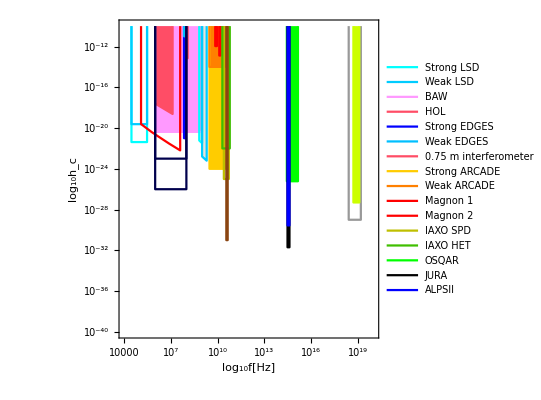

```mathematica
DetectorsPlot=ListLogLogPlot[{LSStrong,LSWeak,BAW,HOL,StrongEDGES,WeakEDGES,Akutsu,StrongARCADE,WeakARCADE,Magnon1,Magnon2,IAXOSPD,IAXOHET,OSQAR,JURA,ALPSII,IAXO,CAST,GaussianBeam,DMR,SCRF,SCRF2,ADMX,SQMS},Joined->True,Frame->True,PlotRange->{{10^4,10^20},{10^-40,10^-10}},Filling->Top,InterpolationOrder->1,PlotStyle->DetectorColors,FillingStyle->FillingSt,PlotLegends->DetectorLegends,FrameLabel->{"log_10f[Hz]","log_10h_c"},LabelStyle->Directive[Font->Times,FontSize->16,Black],ImageSize->400,AspectRatio->1]
```

### Strain curves

#### ADLIGO

```mathematica
ClearAll[ShLIGOO3,ShLIGOO2,ShALIGO];
ShALIGO[f_]:=(1.77622*^-47+(5.512413929853313*^-41)/f^4-1.0496430281166838*^-49 f^(3/4)+7.27085548329759*^-52 f^(3/2)+1.2313750485577433*^-54 f^(9/4))
ShLIGOO2[x_]:=(10^(14.476276959061144 -32.893178060113755 Log[x]+11.801605927152258 Log[x]^2-2.217218878073226 Log[x]^3+0.22766981196692465 Log[x]^4-0.011897774172689817 Log[x]^5+0.00024229327914560746 Log[x]^6))^2
ShLIGOO3[x_]:=(10^(25.77458489800254-42.777002215003485 Log[x]+15.115559976728369 Log[x]^2-2.7411465560250083 Log[x]^3+0.26366033980158765 Log[x]^4-0.012290611495338137 Log[x]^5+0.00020067406076950195 Log[x]^6))^2
```

#### ETD

```mathematica
ClearAll[ShETFIT,ShET]
ETSD=Import["Data_Tabs/ET-0000A-18_ETDSensitivityCurveTxtFile.txt","Table"]; 
tbETtab=Table[{ETSD[[ind,1]],ETSD[[ind,4]]},{ind,1,Length[ETSD]}];
inddx=20;
fffx=Sum[c[ii] x^ii,{ii,0,inddx}];
parmsfffx=Table[c[ii],{ii,0,inddx}];
sol1=FindFit[Log10@tbETtab,fffx,parmsfffx,x];
ShETFIT[f_]:=10^(2 fffx)/.sol1/.{x->Log10[f]};
ShET = Interpolation[tbETtab[[1;;-1;;13]]/.{{x_,y_}->{x,y^2}},InterpolationOrder->1];
```

#### LISA

```mathematica
mins =3.33564 10^-9 (*s*);
L= 2.5 10^9(*m *) mins;
A1 = 10/(3 L^2);
fstar=19.09 10^-3;
POMS[f_]:=(1.5 10^-11 mins)^2(1+ ((2 10^-3)/f)^4)
PACC[f_]:=(3 10^-15 mins)^2(1+ ((0.4 10^-3)/f)^2)(1+ (f/(8 10^-3))^4)
Snins[f_]:= A1 ( POMS[f]+2 (1+(Cos[f/fstar])^2)PACC[f]/(2 π f)^4) (1+6/10(f/fstar)^2)
A2=9 10^-45;
αpsd=0.171;
βpsd=292;
κpsd=1020;
γpsd=1680;
fkpsd=0.00215;
SnWDN[f_]:=A2 f^(-7/3)Exp[-f^αpsd+βpsd f Sin[κpsd f]](1+ Tanh[γpsd(fkpsd-f)])
ClearAll[ShLISA];
ShLISA[f_]:=(1/f^6(1.4783014446745445*^-57+1.116181792733409*^-50 f^2+1.873389405547497*^-47 f^4+1.2225630320491557*^-40 f^6+2.0128366993353335*^-37 f^8+(4.9276714822484815*^-58+3.08060597577803*^-51 f^2+5.1909255591048335*^-48 f^4+7.52101068305183*^-43 f^6+1.2379445995014043*^-39 f^8) Cos[104.76689366160294 f]+ⅇ^(-f^0.171+292 f Sin[1020 f]) f^(11/3) (9.000000000000001*^-45-9.000000000000001*^-45 Tanh[1680. (-0.00215+f)]))
)
```

### Preliminaries

```mathematica
pltHFGWC=ListLogLogPlot[{LSStrong,LSWeak,BAW,HOL,StrongEDGES,WeakEDGES,Akutsu,StrongARCADE,WeakARCADE,Magnon1,Magnon2,IAXOSPD,IAXOHET,OSQAR,JURA,ALPSII,IAXO,CAST,GaussianBeam,DMR,ADMX,SQMS(*,SCRF,SCRF2*)},InterpolationOrder->1,Joined->True,Frame->True,PlotRange->{{10^4,10^20},{10^-40,10^-10}},Filling->Top,PlotStyle->DetectorColors,FillingStyle->FillingSt,(*PlotLegends->DetectorLegends,*)LabelStyle->Directive[Font->Times,FontSize->16,Black]];
pltHFGWC2=Quiet@LogLogPlot[{UnitStep[.5-f] √(f ShLISA[f]),UnitStep[f-10] √(f ShALIGO[f]),UnitStep[f-1] √(f ShET[f])},{f,10^-5,10^4},PlotStyle->{{Black,AbsoluteThickness[2]},{Black,Dashing[Small],AbsoluteThickness[2]},{Black,Dashing[Medium],AbsoluteThickness[2]}}];
listhg={Inset[Rotate[Text[Style["LISA",Black,FontFamily->"CMU Serif",12]],0 Degree],Log@{10^-2.2,10^-19},{0,0}],
Inset[Rotate[Text[Style["Ad. LIGO",Black,FontFamily->"CMU Serif",12]],0 Degree],Log@{10^2.,10^-20.8},{0,0}],
Inset[Rotate[Text[Style["ET",Black,FontFamily->"CMU Serif",12]],0 Degree],Log@{10^1.,10^-19},{0,0}],
Inset[Rotate[Text[Style["LSD",Black (*RGBColor[0,0.8,1]*),FontFamily->"CMU Serif",12]],90 Degree],Log@{10^5.,10^-20.4},{0,0}],
Inset[Rotate[Text[Style["BAW",Black (*RGBColor[0,0.8,1]*),FontFamily->"CMU Serif",12]],0 Degree],Log@{10^6.8,10^-19.9},{0,0}],
Inset[Rotate[Text[Style["HOL",Black (*RGBColor[0,0.8,1]*),FontFamily->"CMU Serif",12]],90 Degree],Log@{10^6.8,10^-17},{0,0}],
Inset[Rotate[Text[Style["EDGES",Black (*RGBColor[0,0.8,1]*),FontFamily->"CMU Serif",12]],90 Degree],Log@{10^8.3,10^-17.6},{0,0}],
Inset[Rotate[Text[Style["ARCADE",Black (*RGBColor[0,0.8,1]*),FontFamily->"CMU Serif",12]],90 Degree],Log@{10^10,10^-19},{0,0}],
Inset[Rotate[Text[Style["IAXO HET",Black (*RGBColor[0,0.8,1]*),FontFamily->"CMU Serif",12]],90 Degree],Log@{10^11.12,10^-19},{0,0}],
Inset[Rotate[Text[Style["IAXO SPD",Black (*RGBColor[0,0.8,1]*),FontFamily->"CMU Serif",12]],90 Degree],Log@{10^11.1,10^-23},{0,0}],
Inset[Rotate[Text[Style["GB",Black (*RGBColor[0,0.8,1]*),FontFamily->"CMU Serif",12]],0 Degree],Log@{10^10.6,10^-31.4},{0,0}],
Inset[Rotate[Text[Style["OSQAR",Black (*RGBColor[0,0.8,1]*),FontFamily->"CMU Serif",12]],90 Degree],Log@{10^15.,10^-21},{0,0}],
Inset[Rotate[Text[Style["ALPSII",Black (*RGBColor[0,0.8,1]*),FontFamily->"CMU Serif",12]],90 Degree],Log@{10^15.,10^-26.5},{0,0}],
Inset[Rotate[Text[Style["JURA",Black (*RGBColor[0,0.8,1]*),FontFamily->"CMU Serif",12]],0 Degree],Log@{10^13.8,10^-31.},{0,0}],
Inset[Rotate[Text[Style["CAST",Black (*RGBColor[0,0.8,1]*),FontFamily->"CMU Serif",12]],90 Degree],Log@{10^19,10^-25},{0,0}],
Inset[Rotate[Text[Style["IAXO",Black (*RGBColor[0,0.8,1]*),FontFamily->"CMU Serif",12]],90 Degree],Log@{10^19,10^-28.1},{0,0}],
Inset[Rotate[Text[Style["DMR",Black (*RGBColor[0,0.8,1]*),FontFamily->"CMU Serif",12]],-34 Degree],Log@{10^7.03,10^-21.25},{0,0}],(*,
Inset[Rotate[Text[Style["SCRF",Black (*RGBColor[0,0.8,1]*),FontFamily->"CMU Serif",12]],0 Degree],Log@{10^7.,10^-22.5},{0,0}]*)
Inset[Rotate[Text[Style["ADMX",Black (*RGBColor[0,0.8,1]*),FontFamily->"CMU Serif",12]],90 Degree],Log@{10^8.67,10^-19.5},{0,0}],
Inset[Rotate[Text[Style["SQMS",Black (*RGBColor[0,0.8,1]*),FontFamily->"CMU Serif",12]],90 Degree],Log@{10^8.81,10^-22.3},{0,0}]};
AT3=AbsoluteThickness[3];
col=Table[ColorData[{"StarryNightColors","Reverse"}][x],{x,0.,1,1/10}];
frmtt={{MaTeX["h_c",Magnification->2],""},{MaTeX["f\\ [{\\rm Hz}]",Magnification->2],MaTeX["\\log_{10} (m_\\text{\\tiny PBH}/M_\\odot) =\\qquad \\qquad  \\qquad \\qquad \\qquad \\qquad \\qquad \\qquad",Magnification->1.7]}};
frmtt2={{MaTeX["h_0",Magnification->2],""},{MaTeX["f\\ [{\\rm Hz}]",Magnification->2],MaTeX["\\log_{10} (m_\\text{\\tiny PBH}/M_\\odot) =\\qquad \\qquad  \\qquad \\qquad \\qquad \\qquad \\qquad \\qquad",Magnification->1.7]}};
```

### SGWB

```mathematica
With[{namff="Data_Tabs/comp_SGWB_1.m"},Get[namff];]
```

```mathematica
tbplogt={
tab1em6,tab1em6fm1,tab1em7,tab1em7fm1,tab1em8,tab1em8fm1,tab1em9,tab1em9fm1,tab1em10,tab1em10fm1,tab1em11,tab1em11fm1,tab1em12,tab1em12fm1,tab1em13,tab1em13fm1,tab1em14,tab1em14fm1,
tab1em15,tab1em15fm1,tab1em16,tab1em16fm1};
```

```mathematica
pltggTTT=Table[
Join[{{10^4,tempx=tbplogt[[2 ind+1,1,1]];tempy=hc[tbplogt[[2 ind+1,1,2]],tempx];
tempy (√(x^(2/3)x^-2)/.{x->10^4})/(√(x^(2/3)x^-2)/.{x->tempx})}},tbplogt[[2 ind+1]]/.{{x_,y_}->{x,hc[y,x]}}]
,{ind,0,Length[tbplogt]/2-1}];
pltggTTT2=Table[
Join[{{10^4,tempx=tbplogt[[2 ind+1,1,1]];tempy=√(10^5)hc[tbplogt[[2 ind+1,1,2]],tempx];
tempy (√(x^(2/3)x^-2)/.{x->10^4})/(√(x^(2/3)x^-2)/.{x->tempx})}},tbplogt[[2 ind+1]]/.{{x_,y_}->{x,√(10^5)hc[y,x]}}]
,{ind,0,Length[tbplogt]/2-1}];
```

```mathematica
pltggT=Flatten[Join[Table[{{AT3,col[[ind]]}(*,{AT3,col[[ind]],Dashed}*)},{ind,1,Length[col]}]],1];
```

```mathematica
hc[Ωgw_,f_]:=1.9 10^-31(f/10^9)^-1(Ωgw/10^-7)^(1/2)
tbll=Table[{x,-60},{x,1,3}];
plt1=Show[ListLogLogPlot[pltggTTT,InterpolationOrder->1,ImageSize->800,AspectRatio->1/2,ImagePadding->{{lp,rp},{lp,2rp}},
FrameLabel->{{MaTeX["h_c",Magnification->2],""},{MaTeX["f\\ [{\\rm Hz}]",Magnification->2],MaTeX["\\log_{10} (M_c/M_\\odot) =\\qquad \\qquad  \\qquad \\qquad \\qquad \\qquad \\qquad \\qquad",Magnification->1.7]}},FrameTicks->{{llabLin2,ltickLin2},{llabLin2,ltickLin2}},
(*PlotLegends->Placed[LineLegend[MaTeX[{"f_\\text{\\tiny PBH}=1","f_\\text{\\tiny PBH}=0.1","f_\\text{\\tiny PBH}=1\\text{ and } R_\\text{\\tiny max}" },Magnification->1.5],Spacings->{0.1,-0.2}] ,{.23,.22}],*)
PlotStyle->pltggT,PlotRange->{{10^-5,10^20},{10^-38,10^-16}},
PlotLegends->Placed[BarLegend[{"StarryNightColors",{-16,-6}},Table[x,{x,-16,-6,1}],LegendMarkerSize->440,LegendMargins->{{330,0},{-35,0}},LabelStyle->{FontFamily->"CMU Serif",FontSize->15,Black}],Above],
Epilog->Join[{ddx=-0.05;ddy=-0.05;dfy=0.09;
{{Black,AT3,Line[{Scaled[{.10+ddx,.12+ddy}],Scaled[{.15+ddx,.12+ddy}],Scaled[{.16+ddx,.12+ddy}]}]}},
Text[MaTeX["f_\\text{\\tiny PBH}=1",Magnification->1.5],Scaled[{.2+ddx,.12+ddy }],{-1,0}],
{{Black,(*AT3,*)Line[{Scaled[{.10+ddx,.12+ddy+dfy}],Scaled[{.15+ddx,.12+ddy+dfy}],Scaled[{.16+ddx,.12+ddy+dfy}]}]}},
Text[MaTeX["f_\\text{\\tiny PBH}=1\\text{ and } R_\\text{\\tiny PBH}^\\text{\\tiny max}",Magnification->1.5],Scaled[{.2+ddx,.12+ddy +dfy}],{-1,0}]},listhg]
],
ListLogLogPlot[pltggTTT2,InterpolationOrder->1,
PlotStyle->Flatten[Join[Table[{{AbsoluteThickness[1],col[[ind]]}},{ind,1,Length[col]}]],1]],
LogLogPlot[.5 10^-24 √(x^(2/3)x^-2),{x,10^-5,10^3.8},PlotStyle->{Black, AbsoluteThickness[1], Dashed}],
LogLogPlot[150 10^-24 √(x^(2/3)x^-2),{x,10^-5,10^3.8},PlotStyle->{Black, AbsoluteThickness[1], Dashed}],
pltHFGWC,pltHFGWC2
]
```

-Graphics-

### Single event

```mathematica
Get["Data_Tabs/listhciso.m"];
Get["Data_Tabs/listtb1tm.m"];
lispl=lispl[[5;;-1]];
tb1t=tb1t[[3;;-1]];
tb1t1s=tb1t1s[[3;;-1]];
tb1t1millis=tb1t1millis[[3;;-1]];
tb1t1e9yr=tb1t1e9yr[[3;;-1]];
lisplcut={};
AppendTo[lisplcut,lispl[[1,17;;-1]]];
AppendTo[lisplcut,lispl[[2,17;;-1]]];
AppendTo[lisplcut,lispl[[3,17;;-1]]];
AppendTo[lisplcut,lispl[[4,17;;-1]]];
AppendTo[lisplcut,lispl[[5,16;;-1]]];
AppendTo[lisplcut,lispl[[6,16;;-1]]];
AppendTo[lisplcut,lispl[[7,15;;-1]]];
AppendTo[lisplcut,lispl[[8,15;;-1]]];
AppendTo[lisplcut,lispl[[9,14;;-1]]];
AppendTo[lisplcut,lispl[[10,14;;-1]]];
AppendTo[lisplcut,lispl[[11,13;;-1]]];
AppendTo[lisplcut,lispl[[12,13;;-1]]];
AppendTo[lisplcut,lispl[[13,13;;-1]]];
AppendTo[lisplcut,lispl[[14,13;;-1]]];
AppendTo[lisplcut,lispl[[15,12;;-1]]];
AppendTo[lisplcut,lispl[[16,12;;-1]]];
AppendTo[lisplcut,lispl[[17,11;;-1]]];
AppendTo[lisplcut,lispl[[18,11;;-1]]];
AppendTo[lisplcut,lispl[[19,10;;-1]]];
AppendTo[lisplcut,lispl[[20,10;;-1]]];
AppendTo[lisplcut,lispl[[21,10;;-1]]];
AppendTo[lisplcut,lispl[[22,10;;-1]]];
```

```mathematica
plt1=Show[ListLogLogPlot[lisplcut,InterpolationOrder->1,ImageSize->800,AspectRatio->1/2,ImagePadding->{{lp,rp},{lp,2rp}},
FrameLabel->frmtt,FrameTicks->{{llabLin2,ltickLin2},{llabLin2,ltickLin2}},PlotStyle->Flatten[Join[Table[{{AT3,col[[ind]]},{AT3,col[[ind]],Dashed}},{ind,1,Length[col]}]],1],PlotRange->{{10^-5,10^20},{10^-32,10^-16}},PlotLegends->Placed[BarLegend[{"StarryNightColors",{-16,-6}},9,LegendMarkerSize->440,LegendMargins->{{330,0},{-35,0}},LabelStyle->{FontFamily->"CMU Serif",FontSize->15,Black}],Above],Epilog->Join[{ddx=-0.05;ddy=.04;dfy=0.08;
{{Black,AT3,Dashed,Line[{Scaled[{.10+ddx,.12+ddy}],Scaled[{.15+ddx,.12+ddy}],Scaled[{.16+ddx,.12+ddy}]}]}},
Text[MaTeX["f_\\text{\\tiny PBH}=0.1",Magnification->1.5],Scaled[{.17+ddx,.12+ddy }],{-1,0}],
{{Black,AT3,Line[{Scaled[{.10+ddx,.12+ddy+dfy}],Scaled[{.15+ddx,.12+ddy+dfy}],Scaled[{.16+ddx,.12+ddy+dfy}]}]}},
Text[MaTeX["f_\\text{\\tiny PBH}=1",Magnification->1.5],Scaled[{.17+ddx,.12+ddy +dfy}],{-1,0}]}
,listhg]]
,
ListLogLogPlot[tb1t,Joined->False,PlotStyle->Table[{(*PointSize[0.001],*)col[[ind]]},{ind,1,Length[col]}],
PlotMarkers->(*"⊗"*)□(*■*)(*★*)],
ListLogLogPlot[tb1t1s,Joined->False,PlotStyle->Table[{(*PointSize[0.001],*)col[[ind]]},{ind,1,Length[col]}],
PlotMarkers->(*"⊗"*) ● (*★*)],
ListLogLogPlot[tb1t1millis,Joined->False,PlotStyle->Table[{(*PointSize[0.001],*)col[[ind]]},{ind,1,Length[col]}],
PlotMarkers->(*"⊗"*) "⊙"(*★*)],
ListLogLogPlot[tb1t1e9yr,Joined->False,PlotStyle->Table[{(*PointSize[0.001],*)col[[ind]]},{ind,1,Length[col]}],
PlotMarkers->(*""*)  ■(*★*)],pltHFGWC2,pltHFGWC]
```

-Graphics-

```mathematica
Get["Data_Tabs/listhciso.m"];
Get["Data_Tabs/listtb1tm.m"];
lisplh0=lisplh0[[1;;-1]];
tb1th0=tb1th0[[1;;-1]];
tb1t1sh0=tb1t1sh0[[1;;-1]];
tb1t1millish0=tb1t1millish0[[1;;-1]];
tb1t1e9yrh0=tb1t1e9yrh0[[1;;-1]];
```

```mathematica
lisplcuth0={};
AppendTo[lisplcuth0,lisplh0[[1,17;;-1]]];
AppendTo[lisplcuth0,lisplh0[[2,17;;-1]]];
AppendTo[lisplcuth0,lisplh0[[3,17;;-1]]];
AppendTo[lisplcuth0,lisplh0[[4,17;;-1]]];
AppendTo[lisplcuth0,lisplh0[[5,16;;-1]]];
AppendTo[lisplcuth0,lisplh0[[6,16;;-1]]];
AppendTo[lisplcuth0,lisplh0[[7,15;;-1]]];
AppendTo[lisplcuth0,lisplh0[[8,15;;-1]]];
AppendTo[lisplcuth0,lisplh0[[9,14;;-1]]];
AppendTo[lisplcuth0,lisplh0[[10,14;;-1]]];
AppendTo[lisplcuth0,lisplh0[[11,13;;-1]]];
AppendTo[lisplcuth0,lisplh0[[12,13;;-1]]];
AppendTo[lisplcuth0,lisplh0[[13,13;;-1]]];
AppendTo[lisplcuth0,lisplh0[[14,13;;-1]]];
AppendTo[lisplcuth0,lisplh0[[15,12;;-1]]];
AppendTo[lisplcuth0,lisplh0[[16,12;;-1]]];
AppendTo[lisplcuth0,lisplh0[[17,11;;-1]]];
AppendTo[lisplcuth0,lisplh0[[18,11;;-1]]];
AppendTo[lisplcuth0,lisplh0[[19,10;;-1]]];
AppendTo[lisplcuth0,lisplh0[[20,10;;-1]]];
AppendTo[lisplcuth0,lisplh0[[21,10;;-1]]];
AppendTo[lisplcuth0,lisplh0[[22,10;;-1]]];
AppendTo[lisplcuth0,lisplh0[[23,10;;-1]]];
AppendTo[lisplcuth0,lisplh0[[24,10;;-1]]];
```

```mathematica
AT3=AbsoluteThickness[3];
col=Table[ColorData[{"StarryNightColors","Reverse"}][x],{x,0.,1,1/13}];
plt1=Show[ListLogLogPlot[lisplcuth0,InterpolationOrder->1,ImageSize->800,AspectRatio->1/2,ImagePadding->{{lp,rp},{lp,2rp}},
FrameLabel->frmtt2,FrameTicks->{{llabLin2,ltickLin2},{llabLin2,ltickLin2}},
PlotStyle->Flatten[Join[Table[{{AT3,col[[ind]]},{AT3,col[[ind]],Dashed}},{ind,1,Length[col]}]],1],PlotRange->{{10^-5,10^20},{10^-32,10^-16}},
PlotLegends->Placed[
BarLegend[{"StarryNightColors",{-16,-6}},9(*Table[x,{x,-16,-6,1}]*) (*BarLegend[{"SolarColors",{0,1}},5]*)
,LegendMarkerSize->440,LegendMargins->{{330,0},{-35,0}},LabelStyle->{FontFamily->"CMU Serif",FontSize->15,Black}],Above],
Epilog->Join[{ddx=-0.05;ddy=.04;dfy=0.08;
{{Black,AT3,Dashed,Line[{Scaled[{.10+ddx,.12+ddy}],Scaled[{.15+ddx,.12+ddy}],Scaled[{.16+ddx,.12+ddy}]}]}},
Text[MaTeX["f_\\text{\\tiny PBH}=0.1",Magnification->1.5],Scaled[{.17+ddx,.12+ddy }],{-1,0}],
{{Black,AT3,Line[{Scaled[{.10+ddx,.12+ddy+dfy}],Scaled[{.15+ddx,.12+ddy+dfy}],Scaled[{.16+ddx,.12+ddy+dfy}]}]}},
Text[MaTeX["f_\\text{\\tiny PBH}=1",Magnification->1.5],Scaled[{.17+ddx,.12+ddy +dfy}],{-1,0}]},listhg]],
ListLogLogPlot[tb1th0,Joined->False,PlotStyle->Table[{(*PointSize[0.001],*)col[[ind]]},{ind,1,Length[col]}],
PlotMarkers->(*"⊗"*)□ (*■*)(*★*)],
ListLogLogPlot[tb1t1millish0,Joined->False,PlotStyle->Table[{(*PointSize[0.001],*)col[[ind]]},{ind,1,Length[col]}],
PlotMarkers->(*"⊗"*) "⊙"(*★*)],
ListLogLogPlot[tb1t1sh0,Joined->False,PlotStyle->Table[{(*PointSize[0.001],*)col[[ind]]},{ind,1,Length[col]}],
PlotMarkers->(*"⊗"*) ● (*★*)],
ListLogLogPlot[tb1t1e9yrh0,Joined->False,PlotStyle->Table[{(*PointSize[0.001],*)col[[ind]]},{ind,1,Length[col]}],
PlotMarkers->(*""*)  ■(*★*)],pltHFGWC2,pltHFGWC]
```

-Graphics-